```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
mi1 = INDefine[firstExtreme->2,secondExtreme->4];
```

```mathematica
mi2 = INDefine[firstExtreme->4,secondExtreme->6];
```

```mathematica
ai1=INDefine[firstExtreme->0,secondExtreme->40];
```

```mathematica
ai2=INDefine[firstExtreme->50,secondExtreme->90];
```

```mathematica
cf1=CFDefine[magnitudeInterval->mi1,angleInterval->ai1]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[40],FEI[[],SEI[]]]]

```mathematica
cf2=CFDefine[magnitudeInterval->mi2,angleInterval->ai2]
```

CF[IN[FE[4],SE[6],FEI[[],SEI[]]],IN[FE[50],SE[90],FEI[[],SEI[]]]]

```mathematica
CFProjectionPlot[cf1,cf2];
```

```mathematica
raddition = CFAddition[cf1,cf2]
```

CF[IN[FE[4.47214],SE[9.96347],FEI[[],SEI[]]],IN[FE[25.],SE[78.1243],FEI[[],SEI[]]]]

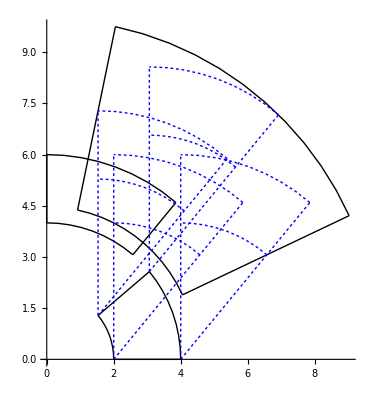
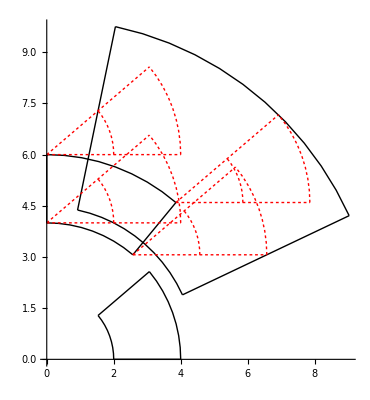

```mathematica
CFAdditionPlot[cf1,cf2,raddition]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf3=CFDefine[magnitudeInterval->INDefine[firstExtreme->2,secondExtreme->4],angleInterval->INDefine[firstExtreme->0,secondExtreme->70]]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[70],FEI[[],SEI[]]]]

```mathematica
cf4=CFDefine[magnitudeInterval->INDefine[firstExtreme->4,secondExtreme->6],angleInterval->INDefine[firstExtreme->30,secondExtreme->70]]
```

CF[IN[FE[4],SE[6],FEI[[],SEI[]]],IN[FE[30],SE[70],FEI[[],SEI[]]]]

```mathematica
CFProjectionPlot[cf3,cf4];
```

```mathematica
cfr2=CFAddition[cf3,cf4]
```

CF[IN[FE[5.04701],SE[10.],FEI[[],SEI[]]],IN[FE[15.],SE[70.],FEI[[],SEI[]]]]

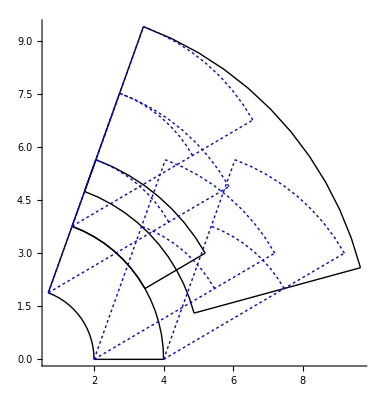
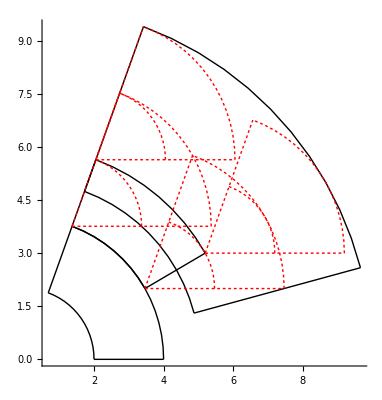

```mathematica
CFAdditionPlot[cf3,cf4,cfr2]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf5=CFDefine[magnitudeInterval->INDefine[firstExtreme->2,secondExtreme->4],angleInterval->INDefine[firstExtreme->0,secondExtreme->2]]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[2],FEI[[],SEI[]]]]

```mathematica
cf6=CFDefine[magnitudeInterval->INDefine[firstExtreme->22,secondExtreme->24],angleInterval->INDefine[firstExtreme->120,secondExtreme->150]]
```

CF[IN[FE[22],SE[24],FEI[[],SEI[]]],IN[FE[120],SE[150],FEI[[],SEI[]]]]

```mathematica
CFProjectionPlot[cf5,cf6];
```

```mathematica
cfr3=CFAddition[cf5,cf6]
```

CF[IN[FE[18.6435],SE[23.1286],FEI[[],SEI[]]],IN[FE[110.045],SE[147.429],FEI[[],SEI[]]]]

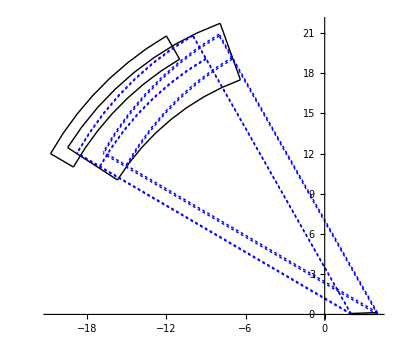
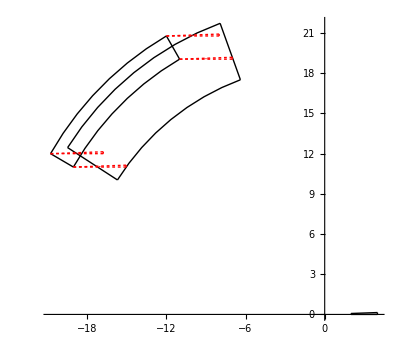

```mathematica
CFAdditionPlot[cf5,cf6,cfr3]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf7=CFDefine[magnitudeInterval->INDefine[firstExtreme->2,secondExtreme->4],angleInterval->INDefine[firstExtreme->0,secondExtreme->1]]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[0],SE[1],FEI[[],SEI[]]]]

```mathematica
cf8=CFDefine[magnitudeInterval->INDefine[firstExtreme->22,secondExtreme->24],angleInterval->INDefine[firstExtreme->180,secondExtreme->270]]
```

CF[IN[FE[22],SE[24],FEI[[],SEI[]]],IN[FE[180],SE[270],FEI[[],SEI[]]]]

```mathematica
cfr4=CFAddition[cf7,cf8]
```

CF[IN[FE[18],SE[24.3311],FEI[[],SEI[]]],IN[FE[179.778],SE[280.335],FEI[[],SEI[]]]]

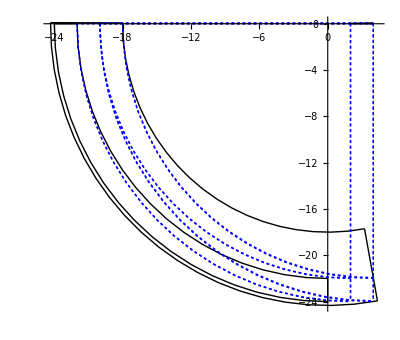
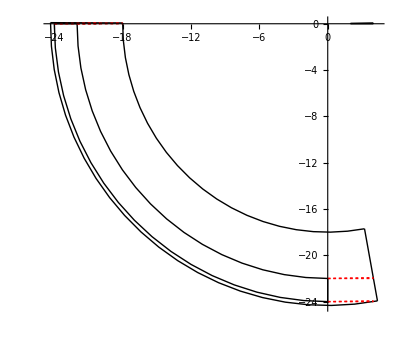

```mathematica
CFAdditionPlot[cf7,cf8,cfr4]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf9=CFDefine[magnitudeInterval->INDefine[firstExtreme->2,secondExtreme->4],angleInterval->INDefine[firstExtreme->0,secondExtreme->360]];
```

```mathematica
cf10=CFDefine[magnitudeInterval->INDefine[firstExtreme->22,secondExtreme->24],angleInterval->INDefine[firstExtreme->90,secondExtreme->270]];
```

```mathematica
CFProjectionPlot[cf9,cf10];
```

```mathematica
res=CFAddition[cf9,cf10]
```

CF[IN[FE[18.],SE[28.],FEI[[],SEI[]]],IN[FE[79.5243],SE[280.476],FEI[[],SEI[]]]]

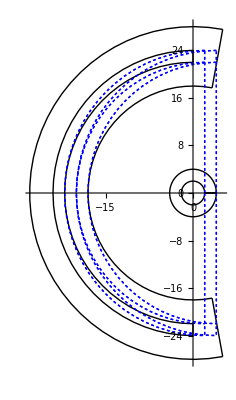
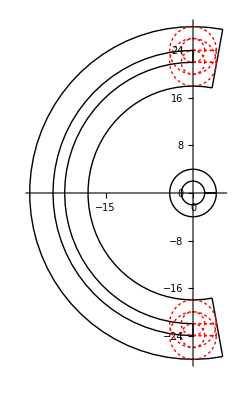

```mathematica
CFAdditionPlot[cf9,cf10,res]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf11=CFDefine[magnitudeInterval->INDefine[firstExtreme->22,secondExtreme->24],angleInterval->INDefine[firstExtreme->180,secondExtreme->90,seIncluded->")"]]
```

CF[IN[FE[22],SE[24],FEI[[],SEI[]]],IN[FE[180],SE[90],FEI[[],SEI[)]]]

```mathematica
cf12=CFDefine[magnitudeInterval->INDefine[firstExtreme->2,secondExtreme->4],angleInterval->INDefine[firstExtreme->90,secondExtreme->180,seIncluded->")"]]
```

CF[IN[FE[2],SE[4],FEI[[],SEI[]]],IN[FE[90],SE[180],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf11,cf12];
```

```mathematica
cfr6=CFAddition[cf11,cf12]
```

CF[IN[FE[18.],SE[28.],FEI[[],SEI[]]],IN[FE[169.695],SE[100.305],FEI[[],SEI[]]]]

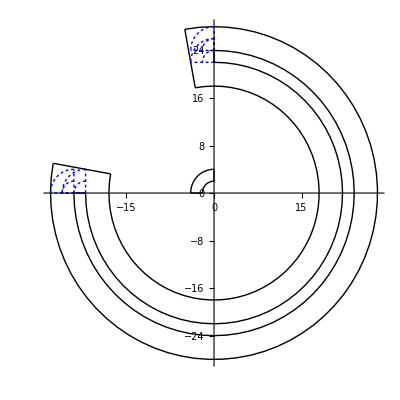
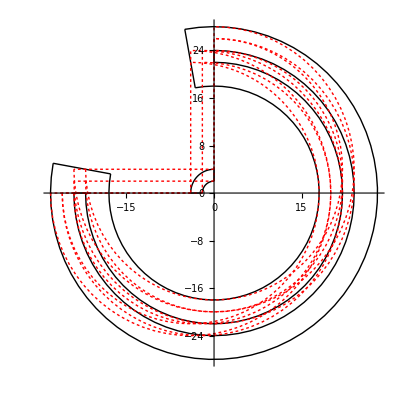

```mathematica
CFAdditionPlot[cf11,cf12,cfr6]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf14=CFDefine[magnitudeInterval->INDefine[firstExtreme->10,secondExtreme->25],angleInterval->INDefine[firstExtreme->0,secondExtreme->135]]
```

CF[IN[FE[10],SE[25],FEI[[],SEI[]]],IN[FE[0],SE[135],FEI[[],SEI[]]]]

```mathematica
cf15=CFDefine[magnitudeInterval->INDefine[firstExtreme->1,secondExtreme->3],angleInterval->INDefine[firstExtreme->150,secondExtreme->285,seIncluded->")"]]
```

CF[IN[FE[1],SE[3],FEI[[],SEI[]]],IN[FE[150],SE[285],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf14,cf15];
```

```mathematica
resadd=CFAddition[cf14,cf15]
```

CF[IN[FE[7.],SE[27.9086],FEI[[],SEI[]]],IN[FE[342.542],SE[152.458],FEI[[],SEI[]]]]

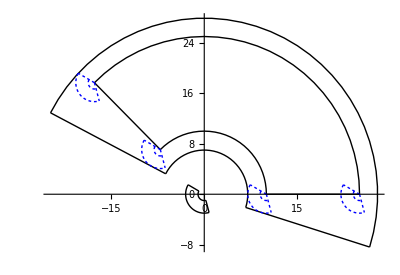
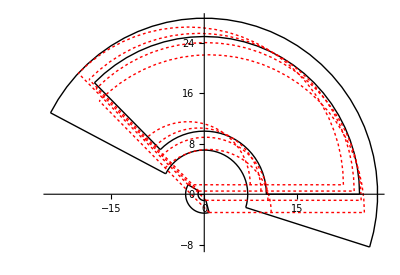

```mathematica
CFAdditionPlot[cf14,cf15,resadd]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf16=CFDefine[magnitudeInterval->INDefine[firstExtreme->10,secondExtreme->25],angleInterval->INDefine[firstExtreme->0,secondExtreme->135]]
```

CF[IN[FE[10],SE[25],FEI[[],SEI[]]],IN[FE[0],SE[135],FEI[[],SEI[]]]]

```mathematica
cf17=CFDefine[magnitudeInterval->INDefine[firstExtreme->13,secondExtreme->15],angleInterval->INDefine[firstExtreme->150,secondExtreme->285,seIncluded->")"]]
```

CF[IN[FE[13],SE[15],FEI[[],SEI[]]],IN[FE[150],SE[285],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf16,cf17];
```

```mathematica
cfr8=CFAddition[cf16,cf17]
```

CF[IN[FE[0.],SE[39.6793],FEI[[],SEI[]]],IN[FE[0],SE[360],FEI[[],SEI[]]]]

```mathematica
CFAdditionPlot[cf16,cf17,cfr8]
```

{-Graphics-,-Graphics-}

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf18=CFDefine[magnitudeInterval->INDefine[firstExtreme->10,secondExtreme->25],angleInterval->INDefine[firstExtreme->60,secondExtreme->30]]
```

CF[IN[FE[10],SE[25],FEI[[],SEI[]]],IN[FE[60],SE[30],FEI[[],SEI[]]]]

```mathematica
cf19=CFDefine[magnitudeInterval->INDefine[firstExtreme->13,secondExtreme->15],angleInterval->INDefine[firstExtreme->150,secondExtreme->125,seIncluded->")"]]
```

CF[IN[FE[13],SE[15],FEI[[],SEI[]]],IN[FE[150],SE[125],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf18,cf19];
```

```mathematica
cfr9=CFAddition[cf18,cf19]
```

CF[IN[FE[0.],SE[40.],FEI[[],SEI[]]],IN[FE[0],SE[360],FEI[[],SEI[]]]]

```mathematica
CFAdditionPlot[cf18,cf19,cfr9]
```

{-Graphics-,-Graphics-}

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf20=CFDefine[magnitudeInterval->INDefine[firstExtreme->10,secondExtreme->25],angleInterval->INDefine[firstExtreme->30,secondExtreme->80]]
```

CF[IN[FE[10],SE[25],FEI[[],SEI[]]],IN[FE[30],SE[80],FEI[[],SEI[]]]]

```mathematica
cf21=CFDefine[magnitudeInterval->INDefine[firstExtreme->7,secondExtreme->18],angleInterval->INDefine[firstExtreme->110,secondExtreme->175,seIncluded->")"]]
```

CF[IN[FE[7],SE[18],FEI[[],SEI[]]],IN[FE[110],SE[175],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf20,cf21];
```

```mathematica
cfr10=CFAddition[cf20,cf21]
```

CF[IN[FE[5.73576],SE[41.5743],FEI[[],SEI[]]],IN[FE[41.772],SE[144.818],FEI[[],SEI[]]]]

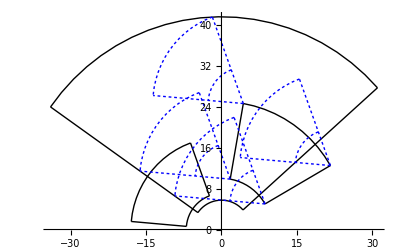
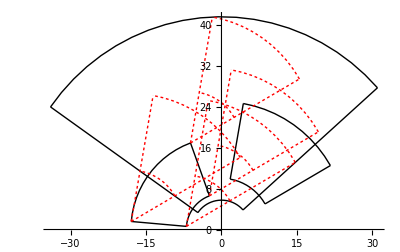

```mathematica
CFAdditionPlot[cf20,cf21,cfr10]
```

```mathematica
<<(NotebookDirectory[]<>"ComplexFans.m")
```

```mathematica
cf22=CFDefine[magnitudeInterval->INDefine[firstExtreme->1,secondExtreme->4],angleInterval->INDefine[firstExtreme->30,secondExtreme->80]]
```

CF[IN[FE[1],SE[4],FEI[[],SEI[]]],IN[FE[30],SE[80],FEI[[],SEI[]]]]

```mathematica
cf23=CFDefine[magnitudeInterval->INDefine[firstExtreme->7,secondExtreme->12],angleInterval->INDefine[firstExtreme->190,secondExtreme->245,seIncluded->")"]]
```

CF[IN[FE[7],SE[12],FEI[[],SEI[]]],IN[FE[190],SE[245],FEI[[],SEI[)]]]

```mathematica
CFProjectionPlot[cf22,cf23];
```

```mathematica
cfr11=CFAddition[cf22,cf23]
```

CF[IN[FE[3.],SE[11.6958],FEI[[],SEI[]]],IN[FE[155.15],SE[276.641],FEI[[],SEI[]]]]

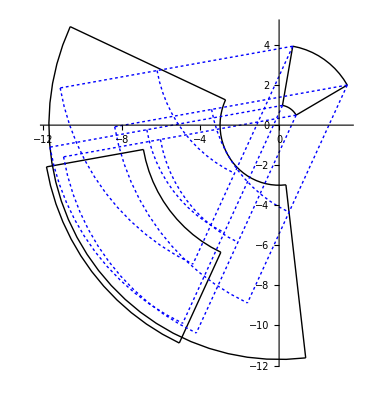
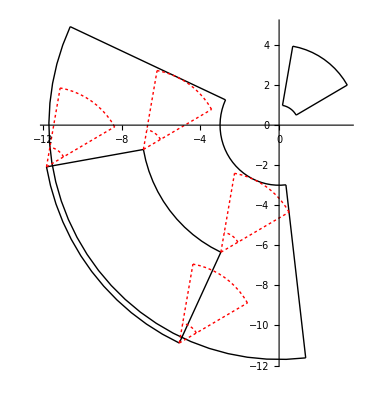

```mathematica
CFAdditionPlot[cf22,cf23,cfr11]
```